# Numerical Integration of the Invertase Reaction

## Numerical integration with NDSolve for analysis of the full, reversible invertase reaction

#### G. Woehlke, Nov. 2017ff

The reaction scheme is the following (E - enzyme, S - sucrose (or ‘Saccharose’ or substrate), ES - enzyme-substrate complex, G - glucose, F - fructose):
-Graphics-

We set up equations from the partial reactions below. Note that we here use r4 and r5 with three participating concentrations, which in reality does not occur. The file MathCode_07_MichaelisMenten_ExtendedSystem.nb addresses this issue.

```mathematica
r1=k12 cE[t]cS[t];
r2=k21 cES[t];
r3=k23 cES[t];
r4=k32G cE[t] cG[t]cF[t];
r5=k32F cE[t] cG[t]cF[t];
```

The biochemical system requires that glucose and fuctose are always present at the same concentrations:

```mathematica
eqEqn={cG[t]==cF[t],cG[t]==10.(*cS[0]*)-cS[t]} (* I don't know why cS[0] does not work... *)
```

{cG[t]==cF[t],cG[t]==10.-cS[t]}

```mathematica
eqnsFulMM={
D[cE[t],t]==-r1 +r2+r3-r4,
D[cES[t],t]==r1-r2-r3+r4,
(*D[cS[t],t]==-r1+r2,*)
(*D[cG[t],t]==+r3-r4,*)     (* mathematically, we may omit the stoichiometric constraints below *)
D[cF[t],t]==+r3-r5
}
```

{cE'[t]==k21 cES[t]+k23 cES[t]-k32G cE[t] cF[t] cG[t]-k12 cE[t] cS[t],cES'[t]==-k21 cES[t]-k23 cES[t]+k32G cE[t] cF[t] cG[t]+k12 cE[t] cS[t],cF'[t]==k23 cES[t]-k32F cE[t] cF[t] cG[t]}

For numerical integration, define the parameters and intital conditions:

The analytical solution does not work...

```mathematica
DSolve[{eqnsFulMM,ic},{cE[t],cES[t],cS[t],cG[t],cF[t]},t]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{{cE'[t]==k21 cES[t]+k23 cES[t]-k32G cE[t] cF[t] cG[t]-k12 cE[t] cS[t],cES'[t]==-k21 cES[t]-k23 cES[t]+k32G cE[t] cF[t] cG[t]+k12 cE[t] cS[t],cF'[t]==k23 cES[t]-k32F cE[t] cF[t] cG[t]},{cE[0]==0.025,cES[0]==0.,cS[0]==10.,cG[0]==0.,cF[0]==0.}},{cE[t],cES[t],cS[t],cG[t],cF[t]},t]

...but the numerical integration does:

```mathematica
params={k12->10.,k21->0.5,k23->25.,k32G->0.25,k32F->1.0};
ic={cE[0]==0.025,cES[0]==0.,cS[0]==10.,cG[0]==0.0,cF[0]==0.0};
tEnd=25.;
```

```mathematica
solFullSystem=NDSolve[{eqnsFulMM,eqEqn,ic}/.params,{cE,cES,cS,cG,cF},{t,0,tEnd}]
```

{{cE→InterpolatingFunction[…],cES→InterpolatingFunction[…],cS→InterpolatingFunction[…],cG→InterpolatingFunction[…],cF→InterpolatingFunction[…]}}

```mathematica
Manipulate[
Plot[Evaluate[{cE[t],cS[t],cES[t],cG[t],cF[t]}/.solFullSystem],{t,0,tEnd},PlotLabel->"Full Michaelis-Menten system \rE + S ⇌ ES ⇌ ... ⇌ E + F + G",PlotStyle->Thickness[thn],
(*PlotStyle->{{Blue,Thickness[thn]},{RGBColor[0.65,0.65,1],Thickness[thn]},{Gray,Dashed},{Gray,Dashed}},*)PlotRange->{{-.05,tEnd},Automatic},AxesLabel->{"time","concentration"},LabelStyle->Directive[FontFamily->Arial,Bold,fs],ImageSize->is]
,
{{is,720,"Image Size"},{450,650,720,900,1050,1280}},
{{thn,0.005,"Line Thickness"},{0.002,0.0035,0.005,0.0067,0.008,0.01}},
{{fs,14,"Font Size"},{9,12,14,18,24}}]
```

Zoom into the indivitual traces. For better visibility of the fast initial phase uncomment  (*LogLogPlot*)and comment out Plot[ ]:

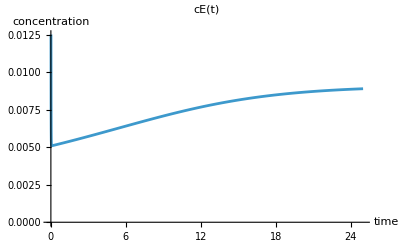
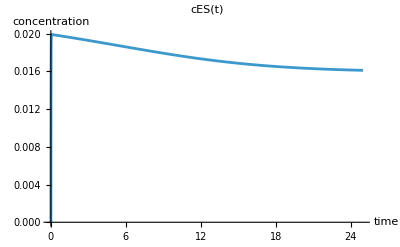
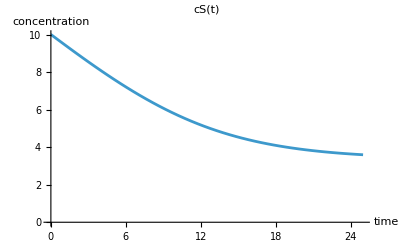
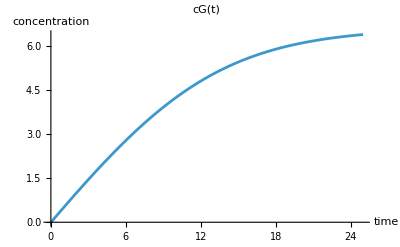
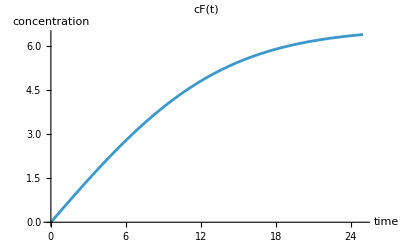

```mathematica
(*LogLogPlot*)Plot[Evaluate[#[t]/.solFullSystem],{t,0,tEnd}, PlotRange->{{-0.05,tEnd},{0,Automatic}},PlotLabel->#[t],AxesLabel->{"time","concentration"}]& /@ {cE,cES,cS,cG,cF}
```